```mathematica
Nmax=10;
Nstep=0.1;
H=DiagonalMatrix[Table[(EC (i+Ng-λ Cos[2π i])^2-ES Cos[2π i]+2 EL/Nstep^2),{i,-Nmax,Nmax,Nstep}]]+DiagonalMatrix[ Table[- EL/Nstep^2,{i,-Nmax,Nmax-Nstep,Nstep}],1]+DiagonalMatrix[ Table[- EL/Nstep^2,{i,-Nmax,Nmax-Nstep,Nstep}],-1];
param={ λ-> 0.6,EC-> 1.0,ES-> 0.7,EL-> 0.1};
param0={ λ-> 0,EC-> 1.0,ES-> 0.7,EL-> 0.1};
```

```mathematica
e10=Table[{Ng,Sort[Eigenvalues[H/.param0]][[1]]},{Ng,-1,1,0.025}];
e20=Table[{Ng,Sort[Eigenvalues[H/.param0]][[2]]},{Ng,-1,1,0.025}];
e30=Table[{Ng,Sort[Eigenvalues[H/.param0]][[3]]},{Ng,-1,1,0.025}];
```

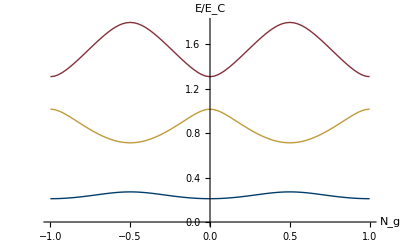

```mathematica
ListPlot[{e10,e20,e30},Joined->True,PlotStyle->{Directive[ Thick,RGBColor["#013D6B"]],Directive[ Thick,RGBColor["#C19B3C"]],Directive[ Thick,RGBColor["#85313C"]]},TicksStyle->Directive[FontSize->16],AxesLabel->{Style["N_g",Bold,21],Style["E/E_C",Bold,21] }]
```

```mathematica
e1=Table[{Ng,Sort[Eigenvalues[H/.param]][[1]]},{Ng,-1,1,0.025}];
e2=Table[{Ng,Sort[Eigenvalues[H/.param]][[2]]},{Ng,-1,1,0.025}];
e3=Table[{Ng,Sort[Eigenvalues[H/.param]][[3]]},{Ng,-1,1,0.025}];
```

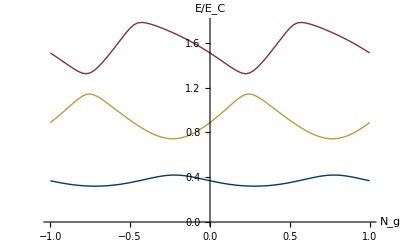

```mathematica
ListPlot[{e1,e2,e3},Joined->True,PlotStyle->{Directive[ Thick,RGBColor["#013D6B"]],Directive[ Thick,RGBColor["#C19B3C"]],Directive[ Thick,RGBColor["#85313C"]]},TicksStyle->Directive[FontSize->16],AxesLabel->{Style["N_g",Bold,21],Style["E/E_C",Bold,21] }]
```